# Gran Test Error

Se analizará de nuevo el error. Esta vez, se implementó el algoritmo MH correctamente

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"MaTeX`"
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/gran_test_error"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/gran_test_error

```mathematica
betas = {10, 50, 100, 250, 500, 750, 1000};
deltas = {0.001, 0.005, 0.01, 0.03, 0.05, 0.07, 0.1};
ene = 20000;
rzs = {0, 0.5, 0.8};
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs;
```

## Objetivo r_z = 0

### p = 0.3

```mathematica
errorDataR0Pp3 = {
	errorsR0Pp3β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas,
	errorsR0Pp3β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.3.wl"][[2,1,10000;;]], targets[[1]], 0.3]]}& /@ deltas	
};
```

```mathematica
Clear[errorsR0Pp3β1, errorsR0Pp3β2, errorsR0Pp3β3, errorsR0Pp3β4, errorsR0Pp3β5, errorsR0Pp3β6, errorsR0Pp3β7]
```

```mathematica
errorVSβDataR0Pp3 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataR0Pp3, betas}]//Transpose;
```

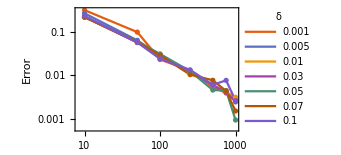
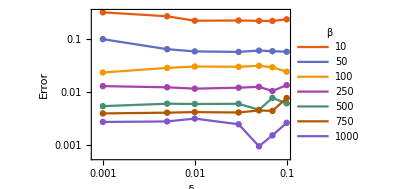

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataR0Pp3, errorDataR0Pp3}, {deltas, betas}, {δ, β}, {β, δ}}]
```

```mathematica
samplesδp001 = Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0_p=0.3.wl"][[2]]& /@ betas;
```

```mathematica
distsδp001 = distsToTarget[#[[1]], targets[[1]], 0.3]& /@ samplesδp001;
```

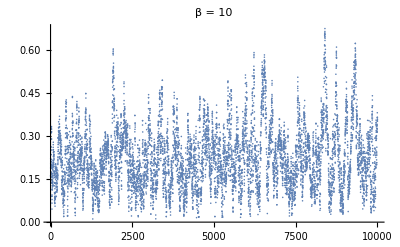
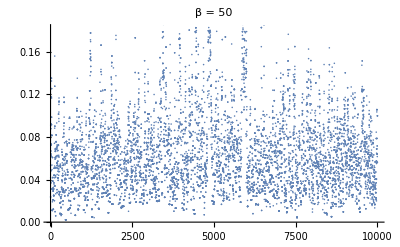
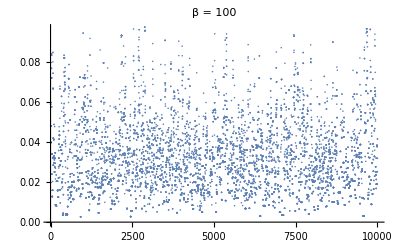
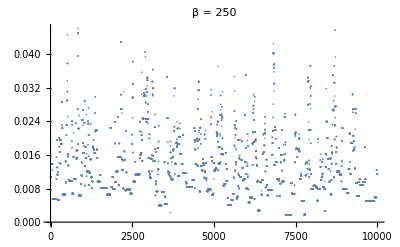
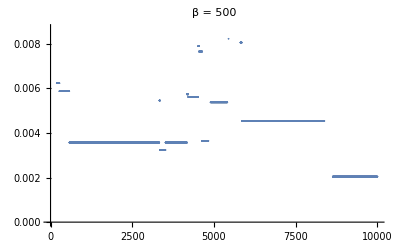
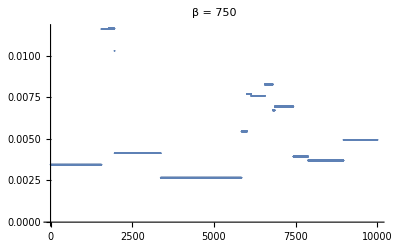
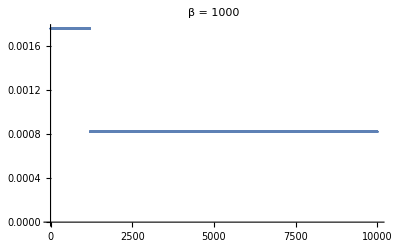

```mathematica
MapThread[ListPlot[#1[[10000;;]], PlotLabel->"β = "<>ToString[#2]]&, {distsδp001, betas}]
```

#### Regresión lineal

```mathematica
regR0Pp3 = LinearModelFit[Log@Flatten[errorVSβDataR0Pp3, 1], x, x]
```

FittedModel[1.00816-0.993399 x]

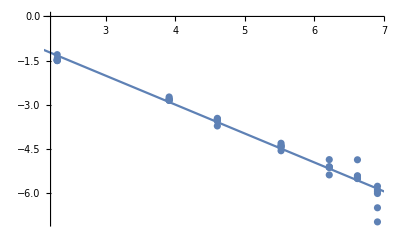

```mathematica
Show[ListPlot[Log@Flatten[errorVSβDataR0Pp3[[2;;]], 1]], Plot[regR0Pp3[x], {x,0, 1000}]]
```

### p = 0.5

```mathematica
errorDataR0Pp5 = {
	errorsR0Pp5β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas,
	errorsR0Pp5β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.5.wl"][[2,1,10000;;]], targets[[1]], 0.5]]}& /@ deltas	
};
```

```mathematica
Clear[errorsR0Pp5β1, errorsR0Pp5β2, errorsR0Pp5β3, errorsR0Pp5β4, errorsR0Pp5β5, errorsR0Pp5β6, errorsR0Pp5β7]
```

```mathematica
errorVSβDataR0Pp5 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataR0Pp5, betas}]//Transpose;
```

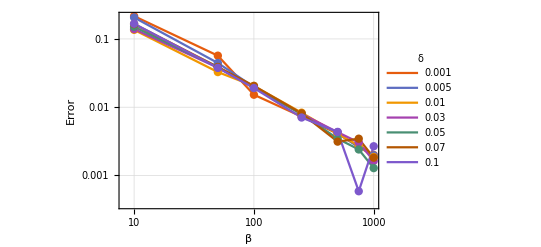
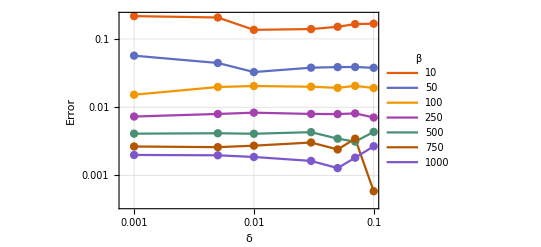

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataR0Pp5, errorDataR0Pp5}, {deltas, betas}, {δ, β}, {β, δ}}]
```

#### Regresión lineal

```mathematica
regR0Pp5 = LinearModelFit[Log[ Flatten[errorVSβDataR0Pp5,1]], x ,x]
```

FittedModel[0.581865-0.992745 x]

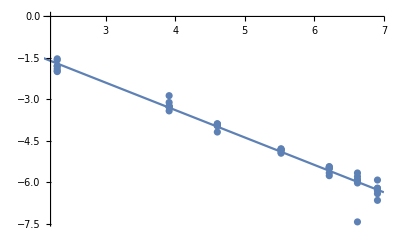

```mathematica
Show[ListPlot[Log@Flatten[errorVSβDataR0Pp5,1]], Plot[regR0Pp5[x], {x, 0, 7}]]
```

### p = 0.8

```mathematica
errorDataR0Pp8 = {
	errorsR0Pp8β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas,
	errorsR0Pp8β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.8.wl"][[2,1,10000;;]], targets[[1]], 0.8]]}& /@ deltas	
};
```

```mathematica
Clear[errorsR0Pp8β1, errorsR0Pp8β2, errorsR0Pp8β3, errorsR0Pp8β4, errorsR0Pp8β5, errorsR0Pp8β6, errorsR0Pp8β7]
```

```mathematica
errorVSβDataR0Pp8 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataR0Pp8, betas}]//Transpose;
```

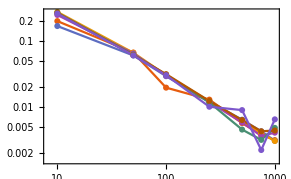
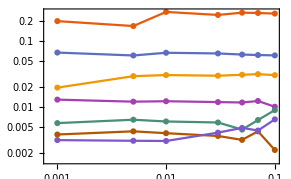

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", 
						 PlotLegends->LineLegend[MaTeX[#2], LegendLabel->MaTeX[#3, Preamble->{"\\usepackage{newtxmath}"}]],
						 FrameStyle->Black,
						 FrameLabel->MaTeX[{#4, "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}], 
						 Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataR0Pp8, errorDataR0Pp8}, {deltas, betas}, {"\\delta", "\\beta"}, {"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Paso}\\,\\,(\\delta)"}}]
```

```mathematica
Export["errorResults_R0Pp8_epsVSdelta.pdf", %298[[2]]]
```

errorResults_R0Pp8_epsVSdelta.pdf

#### Regresión lineal

```mathematica
regR0Pp8 = LinearModelFit[Log[10,Flatten[errorVSβDataR0Pp8,1]], x,x]
```

FittedModel[0.331983-0.938063 x]

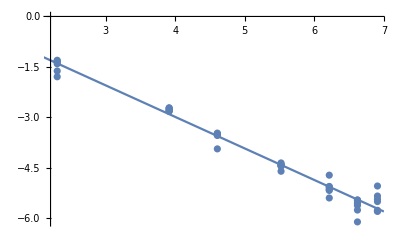

```mathematica
Show[ListPlot[Log@Flatten[errorVSβDataR0Pp8,1]], Plot[regR0Pp8[x], {x, 0, 7}]]
```

## Objetivo r_z= 0.5

### p = 0.3

```mathematica
errorDataRp5Pp3 = {
	errorsRp5Pp3δ1 = {#, Mean[distsToTarget[Get["MHsample_N=50000_delta=0.001_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,40000;;]], targets[[2]], 0.3]]}& /@ betas,
	errorsRp5Pp3δ2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.005_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ betas,
	errorsRp5Pp3δ3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.01_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ betas,
	errorsRp5Pp3δ4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.03_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ betas,
	errorsRp5Pp3δ5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ betas,
	errorsRp5Pp3δ6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.07_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ betas,
	errorsRp5Pp3δ7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.1_beta="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2,1,10000;;]], targets[[2]], 0.3]]}& /@ betas
};
Clear[errorsRp5Pp3δ1, errorsRp5Pp3δ2, errorsRp5Pp3δ3, errorsRp5Pp3δ4, errorsRp5Pp3δ5, errorsRp5Pp3δ6, errorsRp5Pp3δ7]
```

```mathematica
errorVSδDataRp5Pp3 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp5Pp3, deltas}]//Transpose;
```

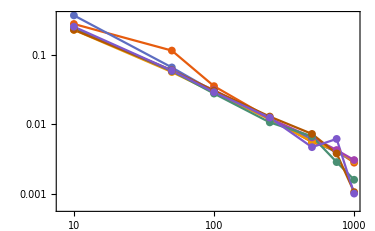
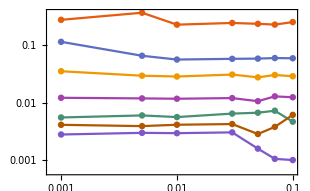

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", 
						 PlotLegends->LineLegend[MaTeX[#2], LegendLabel->#3],
						 FrameLabel->MaTeX[{#4, "\\text{Error}\\,\\,(\\varepsilon)"}, Preamble->{"\\usepackage{newtxmath}"}], 
						 Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic, FrameStyle->Black]&,
		  {{errorDataRp5Pp3, errorVSδDataRp5Pp3}, 
		   {deltas, betas}, 
		   MaTeX[{"\\delta", "\\beta"}, Preamble->{"\\usepackage{newtxmath}"}], {"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Paso}\\,\\,(\\delta)"}}]
```

```mathematica
prueba = Get["MHsample_N=20000_delta=0.05_beta=1000_rz=0.5_p=0.3.wl"][[2]];
```

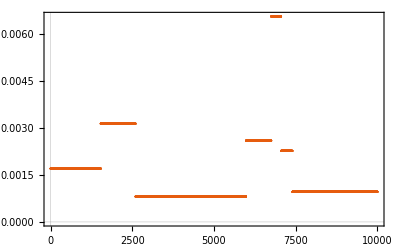

```mathematica
ListPlot[distsToTarget[prueba[[1,10000;;]], targets[[2]], 0.3], PlotTheme->"Scientific",
		 FrameStyle->Black, FrameLabel->MaTeX[{"\\ket{\\psi_i}\\,\\,(i-\\text{ésima iteración})", "d(\\mathcal{C}[\\ket{\\psi_i}], \\varrho_t)"}, Preamble->{"\\usepackage{newtxmath, physics}"}]]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD

```mathematica
Export["errorPlot_Rp5Pp3_lowAccRate.pdf", %316]
```

errorPlot_Rp5Pp3_lowAccRate.pdf

#### Regresión lineal

```mathematica
regRp5Pp3 = LinearModelFit[Log[Flatten[errorDataRp5Pp3,1]], x ,x ]
```

FittedModel[1.13553-1.01997 x]

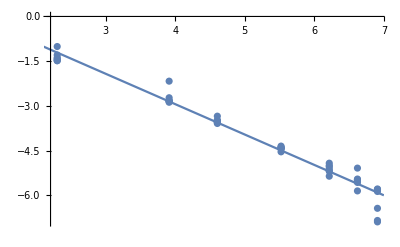

```mathematica
Show[ListPlot[Log[Flatten[errorDataRp5Pp3,1]]], Plot[regRp5Pp3[x], {x, 0, 7}]]
```

### p = 0.5

```mathematica
errorDataRp5Pp5 = {
	errorsRp5Pp5δ1 = {#, Mean[distsToTarget[Get["MHsample_N=50000_delta=0.001_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,40000;;]], targets[[2]], 0.5]]}& /@ betas,
	errorsRp5Pp5δ2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.005_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ betas,
	errorsRp5Pp5δ3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.01_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ betas,
	errorsRp5Pp5δ4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.03_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ betas,
	errorsRp5Pp5δ5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ betas,
	errorsRp5Pp5δ6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.07_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ betas,
	errorsRp5Pp5δ7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.1_beta="<>ToString[#]<>"_rz=0.5_p=0.5.wl"][[2,1,10000;;]], targets[[2]], 0.5]]}& /@ betas 
};
```

```mathematica
Clear[errorsRp5Pp5δ1, errorsRp5Pp5δ2, errorsRp5Pp5δ3, errorsRp5Pp5δ4, errorsRp5Pp5δ5, errorsRp5Pp5δ6, errorsRp5Pp5δ7]
```

```mathematica
errorVSδDataRp5Pp5 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp5Pp5, deltas}]//Transpose;
```

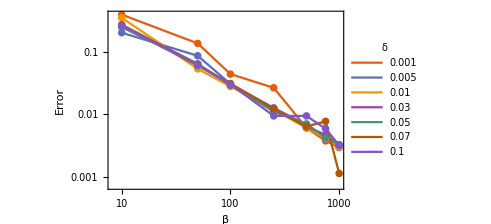
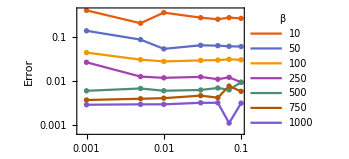

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorDataRp5Pp5, errorVSδDataRp5Pp5}, {deltas, betas}, {δ, β}, {β, δ}}]
```

#### Regresión lineal

```mathematica
regRp5Pp5 = LinearModelFit[Log[Flatten[errorDataRp5Pp5, 1]],x,x]
```

FittedModel[1.08857-0.987515 x]

### p = 0.8

```mathematica
errorDataRp5Pp8 = {
	errorsRp5Pp8β1 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas,
	errorsRp5Pp8β7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.8.wl"][[2,1,10000;;]], targets[[2]], 0.8]]}& /@ deltas
};
```

```mathematica
Clear[errorsRp5Pp8β1, errorsRp5Pp8β2, errorsRp5Pp8β3, errorsRp5Pp8β4, errorsRp5Pp8β5, errorsRp5Pp8β6, errorsRp5Pp8β7]
```

```mathematica
errorVSβDataRp5Pp8 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp5Pp8, betas}]//Transpose;
```

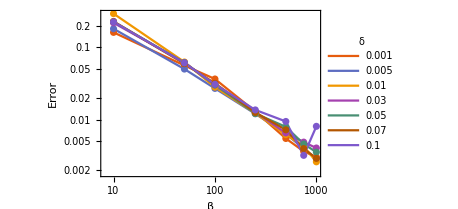
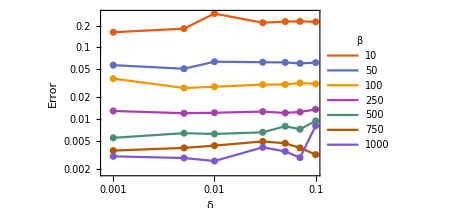

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorVSβDataRp5Pp8, errorDataRp5Pp8}, {deltas, betas}, {δ, β}, {β, δ}}]
```

#### Regresión lineal

```mathematica
regRp5Pp8 = LinearModelFit[Log[Flatten[errorVSβDataRp5Pp8, 1]], x, x]
```

FittedModel[0.66144-0.913879 x]

## Objetivo r_z = 0.8

### p = 0.3

```mathematica
errorDataRp8Pp3 = {
	errorsRp8Pp3δ1 = {#, Mean[distsToTarget[Get["MHsample_N=50000_delta=0.001_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,40000;;]], targets[[3]], 0.3]]}& /@ betas,
	errorsRp8Pp3δ2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.005_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ betas,
	errorsRp8Pp3δ3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.01_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ betas,
	errorsRp8Pp3δ4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.03_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ betas,
	errorsRp8Pp3δ5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ betas,
	errorsRp8Pp3δ6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.07_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ betas,
	errorsRp8Pp3δ7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.1_beta="<>ToString[#]<>"_rz=0.8_p=0.3.wl"][[2,1,10000;;]], targets[[3]], 0.3]]}& /@ betas 
};
```

```mathematica
Clear[errorsRp8Pp3δ1, errorsRp8Pp3δ2, errorsRp8Pp3δ3, errorsRp8Pp3δ4, errorsRp8Pp3δ5, errorsRp8Pp3δ6, errorsRp8Pp3δ7]
```

```mathematica
errorVSδDataRp8Pp3 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp8Pp3, deltas}]//Transpose;
```

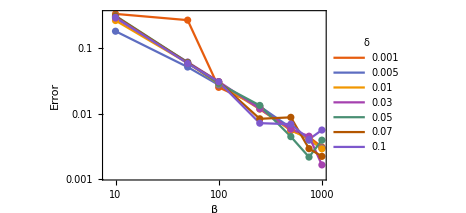
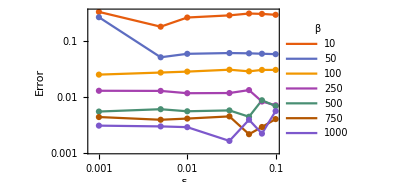

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorDataRp8Pp3, errorVSδDataRp8Pp3}, {deltas, betas}, {δ, β}, {β, δ}}]
```

#### Regresión lineal

```mathematica
regRp8Pp3 = LinearModelFit[Log[Flatten[errorDataRp8Pp3, 1]], x, x]
```

FittedModel[1.11181-1.00656 x]

### p = 0.5

```mathematica
errorDataRp8Pp5 = {
	errorsRp8Pp5δ1 = {#, Mean[distsToTarget[Get["MHsample_N=50000_delta=0.001_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,40000;;]], targets[[3]], 0.5]]}& /@ betas,
	errorsRp8Pp5δ2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.005_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ betas,
	errorsRp8Pp5δ3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.01_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ betas,
	errorsRp8Pp5δ4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.03_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ betas,
	errorsRp8Pp5δ5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ betas,
	errorsRp8Pp5δ6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.07_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ betas,
	errorsRp8Pp5δ7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.1_beta="<>ToString[#]<>"_rz=0.8_p=0.5.wl"][[2,1,10000;;]], targets[[3]], 0.5]]}& /@ betas 
};
```

```mathematica
Clear[errorsRp8Pp5δ1, errorsRp8Pp5δ2, errorsRp8Pp5δ3, errorsRp8Pp5δ4, errorsRp8Pp5δ5, errorsRp8Pp5δ6, errorsRp8Pp5δ7]
```

```mathematica
errorVSδDataRp8Pp5 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp8Pp5, deltas}]//Transpose;
```

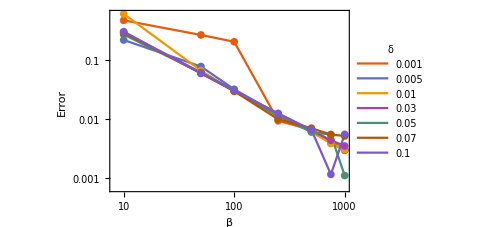
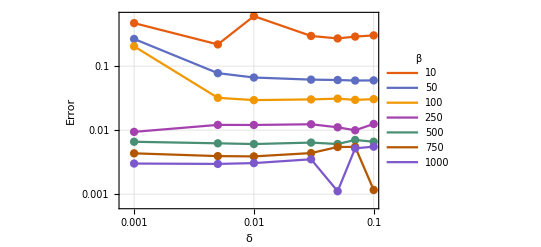

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorDataRp8Pp5, errorVSδDataRp8Pp5}, {deltas, betas}, {δ, β}, {β, δ}}]
```

#### Regresión lineal

```mathematica
regRp8Pp5 = LinearModelFit[Log[Flatten[errorDataRp8Pp5, 1]], x, x]
```

FittedModel[1.41972-1.04498 x]

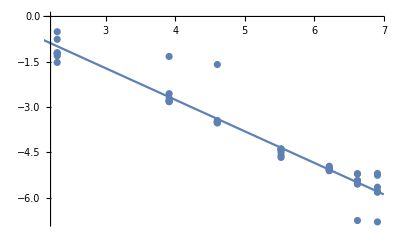

```mathematica
Show[ListPlot[Log[Flatten[errorDataRp8Pp5, 1]]], Plot[1.42 - 1.045 x, {x, 0, 7}]]
```

### p = 0.8

```mathematica
errorDataRp8Pp8 = {
	errorsRp8Pp8δ1 = {#, Mean[distsToTarget[Get["MHsample_N=50000_delta=0.001_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,40000;;]], targets[[3]], 0.8]]}& /@ betas,
	errorsRp8Pp8δ2 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.005_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ betas,
	errorsRp8Pp8δ3 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.01_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ betas,
	errorsRp8Pp8δ4 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.03_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ betas,
	errorsRp8Pp8δ5 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.05_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ betas,
	errorsRp8Pp8δ6 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.07_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ betas,
	errorsRp8Pp8δ7 = {#, Mean[distsToTarget[Get["MHsample_N=20000_delta=0.1_beta="<>ToString[#]<>"_rz=0.8_p=0.8.wl"][[2,1,10000;;]], targets[[3]], 0.8]]}& /@ betas 
};
```

```mathematica
Clear[errorsRp8Pp8δ1, errorsRp8Pp8δ2, errorsRp8Pp8δ3, errorsRp8Pp8δ4, errorsRp8Pp8δ5, errorsRp8Pp8δ6, errorsRp8Pp8δ7]
```

```mathematica
errorVSδDataRp8Pp8 = MapThread[ReplacePart[#1, Table[{i,1}, {i, Length[#1]}] -> #2]&, {errorDataRp8Pp8, deltas}]//Transpose;
```

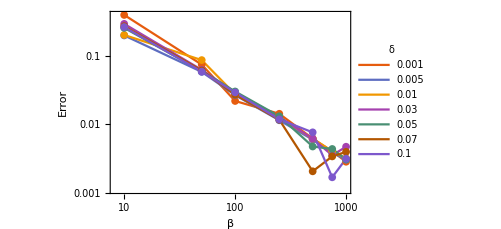
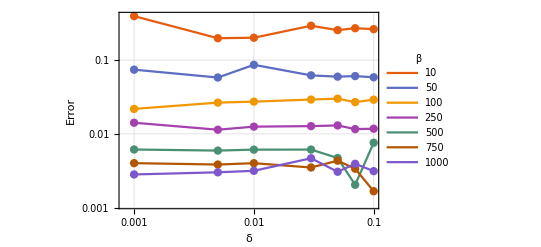

```mathematica
MapThread[ListLogLogPlot[#1, PlotTheme->"Scientific", PlotLegends->LineLegend[#2, LegendLabel->#3],
						 FrameLabel->{#4, "Error"}, Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]&,
		  {{errorDataRp8Pp8, errorVSδDataRp8Pp8}, {deltas, betas}, {δ, β}, {β, δ}}]
```

#### Regresión lineal

```mathematica
regRp8Pp8 = LinearModelFit[Log[Flatten[errorDataRp8Pp8,1]], x,x]
```

FittedModel[1.00047-0.990004 x]

## Proporción de estados aceptados

### Objetivo r_z = 0

#### p = 0.3

```mathematica
accRateDataR0Pp3 = {
	accRatesR0Pp3β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp3β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp3β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp3β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp3β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp3β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp3β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.3.wl"][[2,2]]}& /@ deltas
};
Clear[accRatesR0Pp3β1, accRatesR0Pp3β2, accRatesR0Pp3β3, accRatesR0Pp3β4, accRatesR0Pp3β5, accRatesR0Pp3β6, accRatesR0Pp3β7]
```

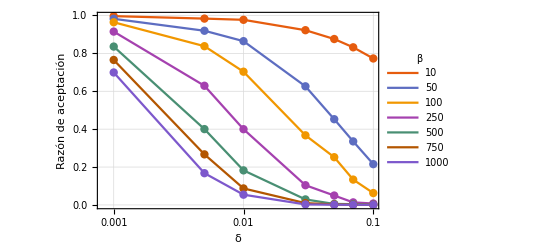

```mathematica
ListLogLinearPlot[accRateDataR0Pp3, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

#### p = 0.5

```mathematica
accRateDataR0Pp5 = {
	accRatesR0Pp5β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp5β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp5β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp5β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp5β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp5β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp5β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.5.wl"][[2,2]]}& /@ deltas
};
Clear[accRatesR0Pp5β1, accRatesR0Pp5β2, accRatesR0Pp5β3, accRatesR0Pp5β4, accRatesR0Pp5β5, accRatesR0Pp5β6, accRatesR0Pp5β7]
```

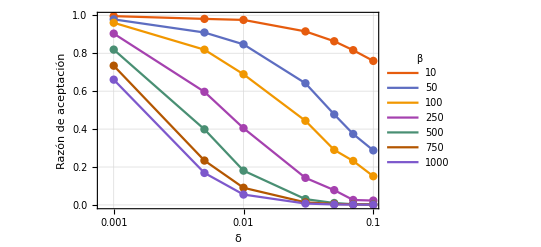

```mathematica
ListLogLinearPlot[accRateDataR0Pp5, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

#### p = 0.8

```mathematica
accRateDataR0Pp8 = {
	accRatesR0Pp8β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp8β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp8β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp8β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp8β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp8β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesR0Pp8β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0_p=0.8.wl"][[2,2]]}& /@ deltas
};
Clear[accRatesR0Pp8β1, accRatesR0Pp8β2, accRatesR0Pp8β3, accRatesR0Pp8β4, accRatesR0Pp8β5, accRatesR0Pp8β6, accRatesR0Pp8β7]
```

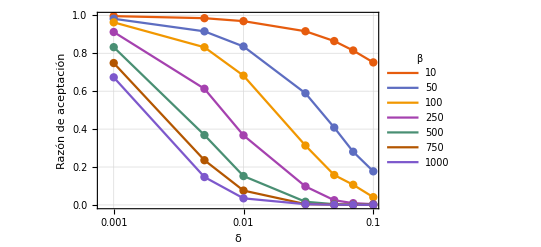

```mathematica
ListLogLinearPlot[accRateDataR0Pp8, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

### Objetivo r_z = 0.5

#### p = 0.3

```mathematica
accRateDataRp5Pp3 = {
	accRatesRp5Pp3β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp3β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp3β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp3β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp3β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp3β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp3β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.3.wl"][[2,2]]}& /@ deltas	
};
Clear[accRatesRp5Pp3β1, accRatesRp5Pp3β2, accRatesRp5Pp3β3, accRatesRp5Pp3β4, accRatesRp5Pp3β5, accRatesRp5Pp3β6, accRatesRp5Pp3β7]
```

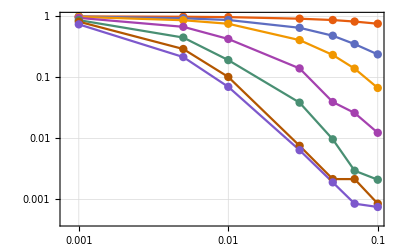

```mathematica
ListLogLogPlot[accRateDataRp5Pp3, 
			      PlotTheme->"Scientific", PlotLegends->LineLegend[MaTeX[betas], LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}]], 
			      FrameLabel->MaTeX[{"\\text{Paso}\\,\\,(\\delta)", "\\text{Razón de aceptación}"}, Preamble->{"\\usepackage{newtxmath}"}], FrameStyle->Black,
			      Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

```mathematica
Directory[]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD

```mathematica
Export["accRatePlot_Rp5Pp3.pdf", %323]
```

accRatePlot_Rp5Pp3.pdf

#### p = 0.5

```mathematica
accRateDataRp5Pp5 = {
	accRatesRp5Pp5β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp5β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp5β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp5β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp5β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp5β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp5β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.5.wl"][[2,2]]}& /@ deltas	
};
Clear[accRatesRp5Pp5β1, accRatesRp5Pp5β2, accRatesRp5Pp5β3, accRatesRp5Pp5β4, accRatesRp5Pp5β5, accRatesRp5Pp5β6, accRatesRp5Pp5β7]
```

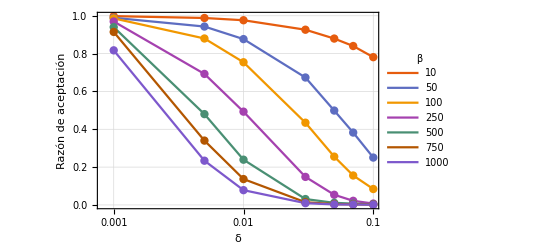

```mathematica
ListLogLinearPlot[accRateDataRp5Pp5, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

#### p = 0.8

```mathematica
accRateDataRp5Pp8 = {
	accRatesRp5Pp8β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp8β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp8β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp8β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp8β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp8β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp5Pp8β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.5_p=0.8.wl"][[2,2]]}& /@ deltas	
};
Clear[accRatesRp5Pp8β1, accRatesRp5Pp8β2, accRatesRp5Pp8β3, accRatesRp5Pp8β4, accRatesRp5Pp8β5, accRatesRp5Pp8β6, accRatesRp5Pp8β7]
```

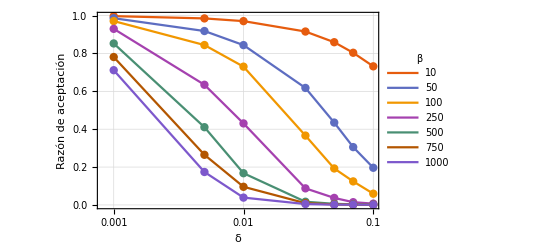

```mathematica
ListLogLinearPlot[accRateDataRp5Pp8, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

### Objetivo r_z = 0.8

#### p = 0.3

```mathematica
accRateDataRp8Pp3 = {
	accRatesRp8Pp3β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp3β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp3β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp3β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp3β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp3β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp3β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.8_p=0.3.wl"][[2,2]]}& /@ deltas
};
Clear[accRatesRp8Pp3β1, accRatesRp8Pp3β2, accRatesRp8Pp3β3, accRatesRp8Pp3β4, accRatesRp8Pp3β5, accRatesRp8Pp3β6, accRatesRp8Pp3β7]
```

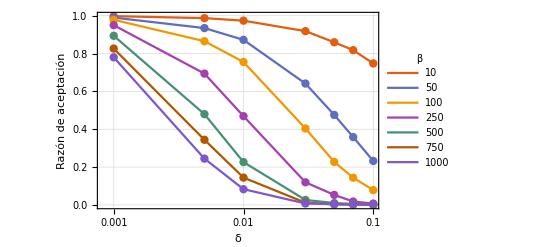

```mathematica
ListLogLinearPlot[accRateDataRp8Pp3, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

#### p = 0.5

```mathematica
accRateDataRp8Pp5 = {
	accRatesRp8Pp5β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp5β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp5β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp5β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp5β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp5β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp5β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.8_p=0.5.wl"][[2,2]]}& /@ deltas
};
Clear[accRatesRp8Pp5β1, accRatesRp8Pp5β2, accRatesRp8Pp5β3, accRatesRp8Pp5β4, accRatesRp8Pp5β5, accRatesRp8Pp5β6, accRatesRp8Pp5β7]
```

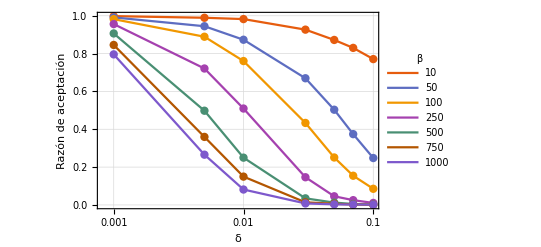

```mathematica
ListLogLinearPlot[accRateDataRp8Pp5, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

#### p = 0.8

```mathematica
accRateDataRp8Pp8 = {
	accRatesRp8Pp8β1 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=10_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp8β2 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=50_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp8β3 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=100_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp8β4 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=250_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp8β5 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=500_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp8β6 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=750_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas,
	accRatesRp8Pp8β7 = {#, Get["MHsample_N=20000_delta="<>ToString[#]<>"_beta=1000_rz=0.8_p=0.8.wl"][[2,2]]}& /@ deltas
};
Clear[accRatesRp8Pp8β1, accRatesRp8Pp8β2, accRatesRp8Pp8β3, accRatesRp8Pp8β4, accRatesRp8Pp8β5, accRatesRp8Pp8β6, accRatesRp8Pp8β7]
```

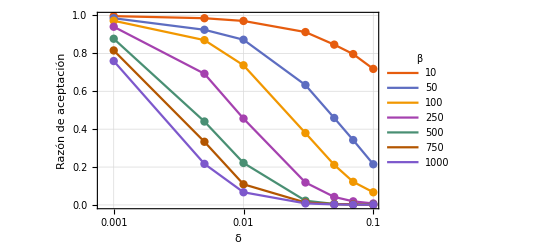

```mathematica
ListLogLinearPlot[accRateDataRp8Pp8, 
			   PlotTheme->"Scientific", PlotLegends->LineLegend[betas, LegendLabel->β], FrameLabel->{"δ", "Razón de aceptación"}, 
			   Joined->True, Mesh->All, MeshStyle->PointSize[0.015], GridLines->Automatic]
```

## Corriendo de nuevo para δ = 0.001

```mathematica
runAndExportMH[N_, β_, δ_, swapP_, rz_]:= With[{targetstate = (IdentityMatrix[2] + rz PauliMatrix[3])/2},
													With[{initialstate = universalInitState},
														sample = Timing[metropolisHastingsSampleGOOD[N, β, δ, swapP, initialstate, targetstate]];
													    Export["MHsample_N="<>ToString[N]<>"_delta="<>ToString[δ]<>"_beta="<>ToString[β]<>"_rz="<>ToString[rz]<>"_p="<>ToString[swapP]<>".wl", sample];
												        Print["Guardada la muestra con: N="<>ToString[N]<>"_delta="<>ToString[δ]<>"_beta="<>ToString[β]<>"_rz="<>ToString[rz]<>"_p="<>ToString[swapP]]
													]
									 		 ]
```

```mathematica
Table[runAndExportMH[50000, i, 0.001, j, k], {i, betas}, {j, swapPs}, {k, rzs}]
```